## Chapter 2: Additional Data Types and Sources

## Introduction

In the first chapter we demonstrated how to build  simple components to track electrical energy consumption by recording register readings from the face of the meter.  In this chapter we will explore how to define components to track other data types, such as records of bulk deliveries of commodities such as fuel oil, or wood. 

We will also explore how to import historical data into the application from a spreadsheet.  If you engage with your school administrators you will probably find that someone at your school has a spreadsheet of monthly utility bills that goes back many years.  Importing data from a spreadsheet will enable you to quickly add your school’s historical energy consumption to your application.  

You may also find that your school’s utility company makes historical bills, or even much finer grained data, available for download from their website.  Take some time to explore the website of your utility company, and keep an eye open for the “Green Button”.  The Green Button Initiative defined a standard data format that many utilities use to enable their customers to download their data.

```mathematica
WebImageSearch["Green Button Initiative","Images",MaxItems->3]
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
WebSearch["Green Button",MaxItems->5]
```

WebSearch::nval: Invalid value for parameter Language in service BingSearch.

Dataset[<>]

At the end of this chapter we will have all of the tools necessary to build an application that can track all of the fuel consumption of a single building.  In Chapter 3 we will pull everything together to deploy a working application.

## User Stories

### Plot Fuel Oil Deliveries Over Time

#### Story Details

As a participant in my school’s energy tracking initiative,  I want to plot my school’s fuel oil deliveries  over time.

#### Background Information

Some energy sources such as fuel oil, or wood, are delivered in large quantities, at irregular intervals, stored on site, and consumed over time.    Plots of the delivery of these commodities over time may benefit from  different presentation than plots of regular time series data due to the irregularity of the deliveries .  For instance, if you wish to create a monthly plot of fuel oil deliveries, you may find that some months have several deliveries, while some have none.  A continuous line plot depicting this type of data can make it difficult to discern when deliveries occur.

It is also worth remembering that the time of delivery and time of consumption are quite different.  In later sections we will examine ways of estimating the time of consumption from the operation time of boilers, or thermostat data that provides information about when fuel is being used.

#### Code Explanation

First, we create a list of time-value pairs that account for the deliveries to a single location over a year.

```mathematica
fueloildeliveries={{DateObject[{2019,1,10}],250},{DateObject[{2019,1,25}],200},{DateObject[{2019,3,5}],370},{DateObject[{2019,3,20}],250},{DateObject[{2019,5,1}],260},{DateObject[{2019,6,30}],150},{DateObject[{2019,8,30}],110},{DateObject[{2019,10,5}],200},{DateObject[{2019,11,15}],220},{DateObject[{2019,12,14}],270}};
```

Now we create a TimeSeries of the data and plot it.

```mathematica
fueloildeliveriesTimeSeries=TimeSeries[fueloildeliveries]
```

TimeSeries[…]

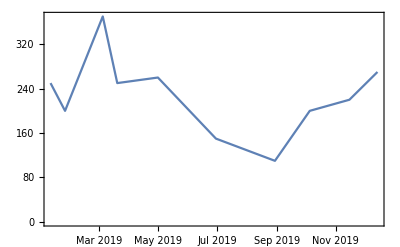

```mathematica
DateListPlot[fueloildeliveriesTimeSeries]
```

Since the data is irregular, it may be useful to regularize the data into monthly totals. The TimeSeriesAggregate function allows us to do that.

```mathematica
fueloildeliveriesTimeSeriesAggregate=TimeSeriesAggregate[TimeSeries[fueloildeliveriesTimeSeries],"Month",Total]
```

TimeSeries[…]

This plot has both the monthly aggregate, and individual delivery time series.

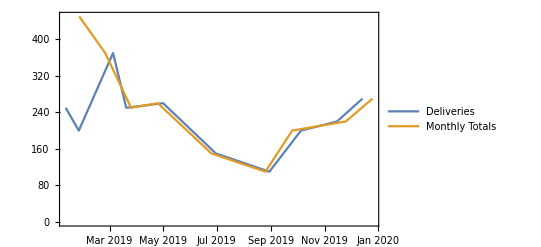

```mathematica
DateListPlot[{fueloildeliveriesTimeSeries,fueloildeliveriesTimeSeriesAggregate},
PlotLegends->{"Deliveries","Monthly Totals"}]
```

An alternate presentation that clarifies each discrete time point is to use the DateListStepPlot.

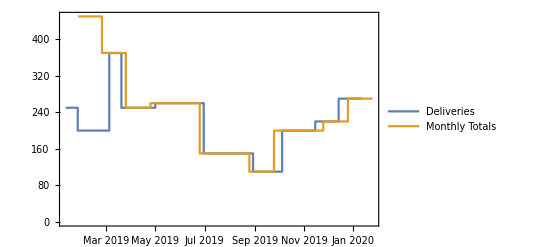

```mathematica
DateListStepPlot[{fueloildeliveriesTimeSeries,fueloildeliveriesTimeSeriesAggregate},PlotLegends->{"Deliveries","Monthly Totals"}]
```

Setting Joined to False on a DateListPlot also clarifies the individual deliveries, and their spacing over time.

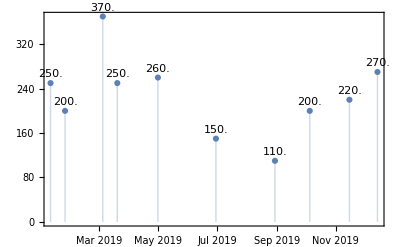

```mathematica
DateListPlot[fueloildeliveriesTimeSeries,
Filling->Axis,
Joined->False,
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotTheme->"Detailed"]
```

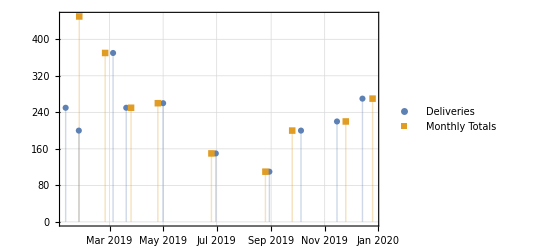

```mathematica
DateListPlot[{fueloildeliveriesTimeSeries,fueloildeliveriesTimeSeriesAggregate},
Filling->Axis,
Joined->False,
PlotMarkers->Automatic,
PlotTheme->"Detailed",
PlotLegends->{"Deliveries","Monthly Totals"}]
```

### Create a form for entering fuel oil deliveries that allows the user to specify the date.

#### Story Details

As a participant  in my school’s energy tracking initiative I want to be able to record fuel oil deliveries in a form, and specify the date that the delivery occurred.

#### Explanation

In Chapter 1 the forms for entering register readings  assumed the date was Yesterday or Today.  In this form we add a new field to specify the date.   The Wolfram Language Interpreter function allows you to specify a wide variety of ways of interpreting a form’s fields.  In this case, we specify that the form be interpreted as a “Date”, which according to the documentation will accept “any standard format or in natural language”.  A “Hint” is added, which suggests the format that the user should enter, although it does not actually restrict the format.

#### Code Explanation

```mathematica
DeleteCloudExpression["fueloildeliveriesCloudExpression"]
```

First, we create a CloudExpression to hold the fuel oil deliveries.

```mathematica
fueloildeliveriesCloudExpression=CreateCloudExpression[fueloildeliveries,"fueloildeliveriesCloudExpression"]
```

CloudExpression[…]

The first Argument of FormPage creates a Date field that will interpret the entered value as a Date.  Try entering Dates in different formats within the Date field to test the flexibility of the Date Interpreter.  This form will add records of fuel oil deliveries to the CloudExpression from the prior story.

```mathematica
fuelOilFormPage=FormPage[
{"Date"-><|Interpreter->"Date","Hint"->"Example January 15, 2019"|>,"Gallons"->"Integer"},
AppendTo[CloudExpression["fueloildeliveriesCloudExpression"],{#Date,#Gallons}]&,
AppearanceRules-><|"Title"->"Enter a fuel oil delivery",
"Description"->"Enter a date and the number of gallons delivered"|>]
```

As you enter new values in the form, evaluate the DateListPlot below to see if the form successfully added a record to the CloudExpression.

```mathematica
DateListPlot[TimeSeries[
Get[CloudExpression["fueloildeliveriesCloudExpression"]]],
Filling->Axis,
Joined->False,
LabelingFunction->(Placed[Last@#1,Above] &),
PlotMarkers->Automatic,
PlotTheme->"Detailed"]
```

-Graphics-

### Import Monthly Bills from a Spreadsheet to a CloudExpression

#### Story Details

-As a participant in my school’s energy tracking initiative I want to be able to import the school’s monthly bill data stored in a spreadsheet into a CloudExpression so that the data can be used by an application, or user with access to the CloudExpression.

#### Background Information

It is likely that someone in your school keeps a spreadsheet with years of utility bill data.  If you can access that spreadsheet, the data in it can be imported into the Wolfram Language and stored in a CloudExpression with a few lines of code.

#### Code Explanation

In this story we will briefly touch upon additional data structures within the Wolfram Language.  In the first chapter we worked with lists of date-value pairs.  We still want to store the data as lists of date-value pairs, but the data will be imported into a Dataset structure, transformed into a structure that uses Associations, and is finally transformed to the list of date-value pairs that we will store in the cloud expression.

Dataset is similar to a typical table structure in a relational database, or even a spreadsheet.  The imported Dataset has columns with column Headers that define the data. The SemanticImport function will import data in a spreadsheet or similar file format, and return a Dataset object.

```mathematica
monthlyBillDataset=SemanticImport["C:\\Users\\kylem\\OneDrive\\Holderness Project\\Computational Sustainability Toolkit\\Sample_Monthly_Bills.csv"]
```

Dataset[<>]

The use of Normal in the code below transforms the Dataset to a list of pairs of Associations.   The

```mathematica
normalmonthlyBillDataset=Normal[monthlyBillDataset]
```

{<|Bill Date→Day: Mon 20 Nov 2017,KWH→1091|>,<|Bill Date→Day: Wed 20 Dec 2017,KWH→941|>,<|Bill Date→Day: Fri 19 Jan 2018,KWH→1258|>,<|Bill Date→Day: Wed 21 Feb 2018,KWH→1134|>,<|Bill Date→Day: Thu 22 Mar 2018,KWH→1036|>,<|Bill Date→Day: Fri 20 Apr 2018,KWH→904|>,<|Bill Date→Day: Tue 22 May 2018,KWH→1045|>,<|Bill Date→Day: Thu 21 Jun 2018,KWH→807|>,<|Bill Date→Day: Tue 24 Jul 2018,KWH→788|>,<|Bill Date→Day: Wed 22 Aug 2018,KWH→482|>,<|Bill Date→Day: Fri 21 Sep 2018,KWH→630|>,<|Bill Date→Day: Mon 22 Oct 2018,KWH→886|>,<|Bill Date→Day: Wed 21 Nov 2018,KWH→744|>,<|Bill Date→Day: Thu 20 Dec 2018,KWH→714|>,<|Bill Date→Day: Mon 21 Jan 2019,KWH→847|>,<|Bill Date→Day: Wed 20 Feb 2019,KWH→729|>,<|Bill Date→Day: Thu 21 Mar 2019,KWH→688|>,<|Bill Date→Day: Mon 22 Apr 2019,KWH→626|>,<|Bill Date→Day: Tue 21 May 2019,KWH→776|>,<|Bill Date→Day: Thu 20 Jun 2019,KWH→1044|>,<|Bill Date→Day: Mon 22 Jul 2019,KWH→1010|>,<|Bill Date→Day: Wed 21 Aug 2019,KWH→961|>,<|Bill Date→Day: Fri 20 Sep 2019,KWH→914|>,<|Bill Date→Day: Mon 21 Oct 2019,KWH→900|>}

The Map function, applies a function to each entry in a list.  In this case the code below takes each pair of associations, and creates a list of pairs of  Bill Date and KWH values.  This is the form that we save in the CloudExpression.

```mathematica
listofMonthlyBills=Map[
		{#["Bill Date"], #["KWH"]} &,
		normalmonthlyBillDataset]
```

{{Day: Mon 20 Nov 2017,1091},{Day: Wed 20 Dec 2017,941},{Day: Fri 19 Jan 2018,1258},{Day: Wed 21 Feb 2018,1134},{Day: Thu 22 Mar 2018,1036},{Day: Fri 20 Apr 2018,904},{Day: Tue 22 May 2018,1045},{Day: Thu 21 Jun 2018,807},{Day: Tue 24 Jul 2018,788},{Day: Wed 22 Aug 2018,482},{Day: Fri 21 Sep 2018,630},{Day: Mon 22 Oct 2018,886},{Day: Wed 21 Nov 2018,744},{Day: Thu 20 Dec 2018,714},{Day: Mon 21 Jan 2019,847},{Day: Wed 20 Feb 2019,729},{Day: Thu 21 Mar 2019,688},{Day: Mon 22 Apr 2019,626},{Day: Tue 21 May 2019,776},{Day: Thu 20 Jun 2019,1044},{Day: Mon 22 Jul 2019,1010},{Day: Wed 21 Aug 2019,961},{Day: Fri 20 Sep 2019,914},{Day: Mon 21 Oct 2019,900}}

```mathematica
DeleteCloudExpression["listofMonthlyBills"]
```

```mathematica
CreateCloudExpression[listofMonthlyBills,"listofMonthlyBills"]
```

CloudExpression[…]

Now we can retrieve the values from the CloudExpression, and plot them.

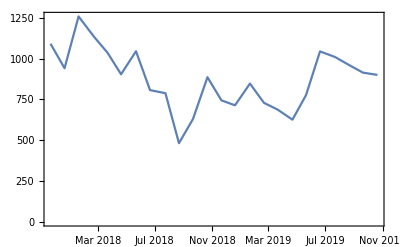

```mathematica
DateListPlot[TimeSeries[Get[CloudExpression["listofMonthlyBills"]]]]
```

Now we can tie the set of functions above into a single operation that we could could use on other spreadsheets.

```mathematica
CreateCloudExpression[
Map[{#["Bill Date"], #["KWH"]} &,Normal[SemanticImport["enter file path"]]],"Monthly Bills"]
```

### Import Interval Data from a Spreadsheet into a New CloudExpression

#### Story Details

-As a participant in my School’s energy tracking initiative I want to be able to  import the interval data that is in a spreadsheet into a new CloudExpression so that the data can be stored in a central location and shared so that other users or applications can view or analyze the data.

#### Background Information

Modern electrical meters, often referred to a “smart meters” are capable of recording, and reporting, energy consumption within relatively short intervals.  Many utilities now program their meters to record intervals of 15 , 30 or 60 minutes.  Many meters are capable of recording intervals as short as 1 minute, but the cost of processing and storing the volume of data resulting from 1 minute intervals is considerable.  

Interval data provides significant insight into how a building uses energy.  You can see when a building uses energy during the day, and infer what the major consumers are at different points of the day.

#### Code Explanation

One can use the same code to import interval data as we used to import monthly bill data.  The primary difference here is that the column headers on the imported file are different, and we name this CloudExpression “Interval Data”.

```mathematica
DeleteCloudExpression["Interval Data"]
```

```mathematica
CreateCloudExpression[
Map[{#["IntervalEnd"], #["Quantity"]} &,Normal[SemanticImport["C:\\Users\\kylem\\OneDrive\\Holderness Project\\Computational Sustainability Toolkit\\Sample_Interval_September.csv"]]],"Interval Data"]
```

CloudExpression[…]

Here we plot the interval data.  Notice the density of the data points.  A meter recording 15 minute interval data generates 96 data points in a day if it is measuring a single time series.  This is 2880 times the number of data points in a month than the single data point  that was available in the era of manually collected meter readings.

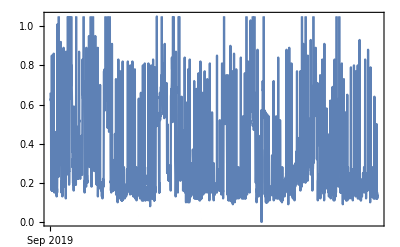

```mathematica
DateListPlot[TimeSeries[Get[CloudExpression["Interval Data"]]]]
```

### Add Interval Data from a Spreadsheet to an Existing CloudExpression

#### Story Details

As a participant in my school’s energy tracking initiative I want to be able to upload interval readings in a spreadsheet to an existing CloudExpression that contains additional interval data.

#### Background Information

In the first story uploading interval data to a CloudExpression we created the CloudExpression, and uploaded a complete list of time-value pairs within the same function.  We require different code to add incremental data to an existing CloudExpression.  We will start with the AppendTo function, as we did adding a single register reading to an existing CloudExpression.  The difference in this case is that we have many more entries to add to the existing CloudExpression.  To accomplish this we will use a form of the Map function paired with a pure function.

#### Code Explanation

First, we will use our code to create a list of time-value pairs of the incremental data that we wish to add.  The spreadsheet used here contains data for the month following the data imported in the prior user story.

```mathematica
incrementalIntervalData=Map[{#["IntervalEnd"], #["Quantity"]} &,Normal[SemanticImport["C:\\Users\\kylem\\OneDrive\\Holderness Project\\Computational Sustainability Toolkit\\Sample_Interval_October.csv"]]]
```

{{Tue 1 Oct 2019 00:15:00GMT-5.,0.13},{Tue 1 Oct 2019 00:30:00GMT-5.,0.13},{Tue 1 Oct 2019 00:45:00GMT-5.,0.15},{Tue 1 Oct 2019 01:00:00GMT-5.,0.11},{Tue 1 Oct 2019 01:15:00GMT-5.,0.17},{Tue 1 Oct 2019 01:30:00GMT-5.,0.15},{Tue 1 Oct 2019 01:45:00GMT-5.,0.14},2867,{Wed 30 Oct 2019 22:45:00GMT-5.,0.82},{Wed 30 Oct 2019 23:00:00GMT-5.,0.71},{Wed 30 Oct 2019 23:15:00GMT-5.,0.64},{Wed 30 Oct 2019 23:30:00GMT-5.,0.66},{Wed 30 Oct 2019 23:45:00GMT-5.,0.62},{Thu 31 Oct 2019 00:00:00GMT-5.,0.64}}
 |  |  |  |

Where we used AppendTo to add new register readings to an existing CloudExpression in the first chapter, that function would be very inefficient in the context of adding thousands of new records to a CloudExpression, as AppendTo returns an updated CloudExpression with each incremental value. This code uses the Put function to fully replace the existing content of CloudExpression “Interval Data” with completely new content.  The new content is a union of the existing data within the CloudExpression and the incrementalIntervalData.

```mathematica
Put[Union[Get[CloudExpression["Interval Data"]],
incrementalIntervalData],
CloudExpression["Interval Data"]]
```

CloudExpression[…]

We can now evaluate the CloudExpression to see an additional month of data has been added.

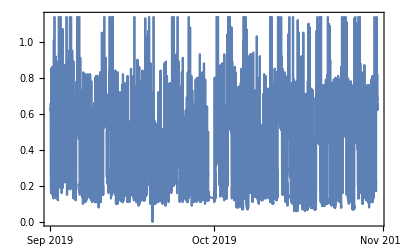

```mathematica
DateListPlot[TimeSeries[Get[CloudExpression["Interval Data"]]]]
```

The code below ties it all together.

```mathematica
Put[Union[Get[CloudExpression["Interval Data"]],
Map[{#["IntervalEnd"], #["Quantity"]} &,
Normal[SemanticImport["C:\\Users\\kylem\\OneDrive\\Holderness Project\\Computational Sustainability Toolkit\\Sample_Interval_October.csv"]]]],
CloudExpression["Interval Data"]]
```

### Use a Form to Add Interval Data from a Spreadsheet to an existing CloudExpression

#### Story Details

-As a participant in my school’s energy tracking initiative I want to be able to upload interval data from a CSV file to an existing CloudExpression through a web form.

#### Code Explanation

This code takes our function that appends interval data to an existing CloudExpression and places it in a FormPage.  The inputs to the page are a CSV file, and the name of the CloudExpression.

```mathematica
intervalDataForm=FormPage[
{"CSV"->"CSV",{"ExpressionName","Expression Name"}->"String"},
Put[Union[Get[CloudExpression[#ExpressionName]],
Map[{#["IntervalEnd"], #["Quantity"]}&,
Normal[SemanticImport[#CSV]]]],
CloudExpression[#ExpressionName]]&,
AppearanceRules-><|"Title"->"Upload a CSV with interval data",
"Description"->"Select a CSV file and provide Cloud Expression name.  The CSV should have columns with headers named IntervalEnd and Quantity."|>]
```

When the form is defined we can CloudDeploy it so that anyone with permission can use it to upload data.

```mathematica
CloudDeploy[intervalDataForm]
```

CloudObject[https://www.wolframcloud.com/obj/48ec0630-bb7c-43b7-a5bb-ce3b4dc5eb92]

We can plot the data again to see that additional data has been added.

```mathematica
Get[CloudExpression["Interval Data"]]
```

{{Sun 1 Sep 2019 00:15:00GMT-5.,0.66},{Sun 1 Sep 2019 00:30:00GMT-5.,0.63},{Sun 1 Sep 2019 00:45:00GMT-5.,0.62},{Sun 1 Sep 2019 01:00:00GMT-5.,0.63},{Sun 1 Sep 2019 01:15:00GMT-5.,0.56},{Sun 1 Sep 2019 01:30:00GMT-5.,0.26},{Sun 1 Sep 2019 01:45:00GMT-5.,0.21},5651,{Wed 30 Oct 2019 22:45:00GMT-5.,0.82},{Wed 30 Oct 2019 23:00:00GMT-5.,0.71},{Wed 30 Oct 2019 23:15:00GMT-5.,0.64},{Wed 30 Oct 2019 23:30:00GMT-5.,0.66},{Wed 30 Oct 2019 23:45:00GMT-5.,0.62},{Thu 31 Oct 2019 00:00:00GMT-5.,0.64}}
 |  |  |  |

```mathematica
DateListPlot[TimeSeries[Get[CloudExpression["Interval Data"]]]]
```

-Graphics-

### Specify the window of interval data displayed in a DateListPlot

#### Story Details

-As a participant in my school’s energy tracking initiative trying to understand how my school consumes electricity, I want to be able to specify the time window of interval data displayed in a DateListPlot or similar visualization function..

#### Background Information

In this story we introduce Manipulate, which is a primary function through which users of the system can manipulate the variables of an expression.  Manipulate

#### Code Explanation

To simplify our code later, first we will define a local TimeSeries object with our CloudExpression data.

```mathematica
intervaldataTimeSeries=TimeSeries[Get[CloudExpression["Interval Data"]]]
```

TimeSeries[…]

If you want to plot only a portion of a TimeSeries, instead of a complete TimeSeries, you apply the TimeSeriesWindow function to a TimeSeries object.  The first argument of the TimeSeriesWindow is the TimeSeries, and the second and third arguments (or perhaps second) are the first time and last time of the window that you wish to select.  First we will plot the complete TimeSeries.

```mathematica
DateListPlot[intervaldataTimeSeries]
```

-Graphics-

Here we will use TimeSeriesWindow to visualize a full day of interval data.

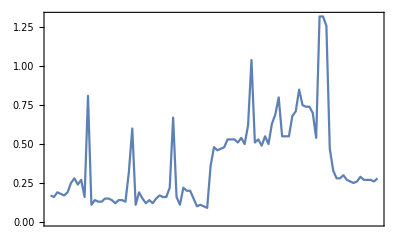

```mathematica
DateListPlot[TimeSeriesWindow[intervaldataTimeSeries,{DateObject[{2019,10,14,0,0}],DateObject[{2019,10,15,0,0}]}]]
```

That works, but we don’t really want to make people type in a date every time they want to select a different window.  We can make the user’s life easier by integrating Manipulate into the expression.  Manipulate is the primary functions that allows users to interact with data on the screen.  The manipulate function allows you to manipulate multiple variables within an expression.  In this case we will allow the user to manipulate both the lower bound, and the upper bound of the TimeSeriesWindow.  To do this, we will take advantage of the TimeSeries properties “FirstTime” and “LastTime”.

To retrieve a property of a TimeSeries you can use the following form.

```mathematica
intervaldataTimeSeries["FirstTime"]
```

3776285700

This output is UnixTime, which is precise, but not exactly meaningful.  To see a human readable value we can wrap that in a DateObject.

```mathematica
DateObject[intervaldataTimeSeries["FirstTime"]]
```

Sun 1 Sep 2019 00:15:00GMT-5.

In a Manipulate expression you specify the variables within the expression that you wish to manipulate, and then you define the parameters for each variable individually.  In this case “a” and “b” define the window of the TimeSeriesWindow function.  The syntax used here to define each variable is {{variable, default value, “label”}, the lower bound of the window, and the upper bound of the window}. Note that the default value, and the lower and upper bounds of the window are defined as the “FirstTime” and “LastTime” of the TimeSeries being visualized.  This ensures that the complete TimeSeries can be viewed, and prevents selection of dates outside of the TimeSeries.

```mathematica
Manipulate[DateListPlot[
TimeSeriesWindow[intervaldataTimeSeries,{a,b}]],
{{a,intervaldataTimeSeries["FirstTime"],"Start Date"},intervaldataTimeSeries["FirstTime"],intervaldataTimeSeries["LastTime"]},{{b,intervaldataTimeSeries["LastTime"],"End Date"},intervaldataTimeSeries["FirstTime"],intervaldataTimeSeries["LastTime"]}]
```

DateListPlot::ldata: TimeSeriesWindow[intervaldataTimeSeries,{3776285700,3781468800}] is not a valid dataset or list of datasets.

Here we will define our first Function.  Functions allow you to simplify the task of composing code that you will use repeatedly.  In the expression below we name the function manipulateDateListPlotTimeSeries, and name the argument timeseries_.  The code of the function is identical to the code above, but “timeseries” is used in every instance within the function that a specific TimeSeries would be specified.  After you evaluate the Function, you can use it with any TimeSeries as the argument.

```mathematica
manipulateDateListPlotTimeSeries[timeseries_]:=Manipulate[DateListPlot[
TimeSeriesWindow[timeseries,{a,b}]],
{{a,timeseries["FirstTime"],"Start Date"},timeseries["FirstTime"],timeseries["LastTime"]},
{{b,timeseries["LastTime"],"End Date"},timeseries["FirstTime"],timeseries["LastTime"]}]
```

```mathematica
manipulateDateListPlotTimeSeries[intervaldataTimeSeries]
```

```mathematica
manipulateDateListPlotTimeSeries[TimeSeries[Get[CloudExpression["Interval Data"]]]]
```

```mathematica
CloudDeploy[Delayed[
manipulateDateListPlotTimeSeries[Get[CloudExpression["Interval Data"]]]]]
```

CloudObject[https://www.wolframcloud.com/obj/8f05dfcb-a33c-4820-ad9f-8cb7d3515250]

```mathematica
CloudObjectInformation[CloudObject["https://www.wolframcloud.com/obj/b3f01761-a460-4540-be31-f76123eed2c9"]]
```